```mathematica
RCWData:={115,235,348,470,587,706,830,938,996,1000}
LCWData:={130,253,385,513,638,762,895,913,918,927}
RCCData:={111,230,341,470,578,696,808,924,1000,1040}
LCCData:={129,253,380,514,637,765,881,931,934,935}
percent:={10,20,30,40,50,60,70,80,90,100}
RCWData2:=Thread[{percent,RCWData}]
LCWData2:=Thread[{percent,LCWData}]
RCCData2:=Thread[{percent,RCCData}]
LCCData2:=Thread[{percent,LCCData}]
ListLinePlot[{RCWData2,RCCData2},PlotLabel->"Right Wheel Speed vs. PWM%",ImageSize->500,GridLines->Automatic,GridLinesStyle->Dashed,AxesLabel->{"%PWM","Frequency [Hz]"}];
```

```mathematica
ListLinePlot[{LCWData2,LCCData2},PlotLabel->"Right Wheel Speed vs. PWM%",ImageSize->500,GridLines->Automatic,GridLinesStyle->Dashed,AxesLabel->{"%PWM","Frequency [Hz]"}];
```

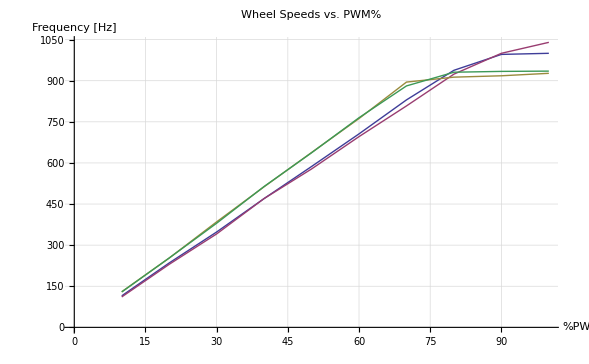

```mathematica
ListLinePlot[{RCWData2,RCCData2,LCWData2,LCCData2},PlotLabel->"Wheel Speeds vs. PWM%",ImageSize->500,GridLines->Automatic,GridLinesStyle->Dashed,AxesLabel->{"%PWM","Frequency [Hz]"}]
```